## This is an example of running a C code from Mathematica

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jinyunlin/QFE-Research/affineFlow-2/JintestCode/testing/ConstantLattice

```mathematica
data = Import["evanres.txt", "table"];
```

```mathematica
ARMS=data[[All, {1, 8}]];
PRMS=data[[All, {1, 9}]];
CRRMS=data[[All, {1, 10}]];
du = data[[All, {1, -4}]];
```

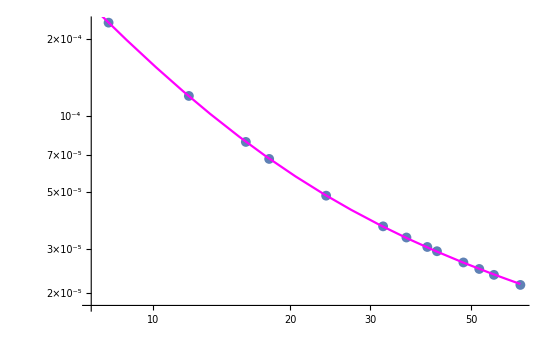

0.0145601/x^2.10887+0.000132393/x^0.460493

```mathematica
QuartFit=NonlinearModelFit[ARMS,a*x^-c+b*x^-d,{a, c, b, d},x];
f1=ListLogLogPlot[ARMS];
f2=LogLogPlot[QuartFit[x], {x,0,64}, PlotStyle->Magenta];
Show[f1,f2]
Normal[QuartFit]
```

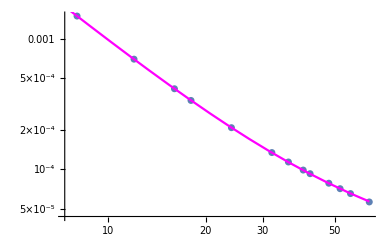

0.0873909/x^1.98383+0.000156643/x^0.367021

```mathematica
QuartFit=NonlinearModelFit[PRMS,a*x^-c+b*x^-d,{a, c, b, d},x];
f1=ListLogLogPlot[PRMS];
f2=LogLogPlot[QuartFit[x], {x,0,64}, PlotStyle->Magenta];
Show[f1,f2]
Normal[QuartFit]
```

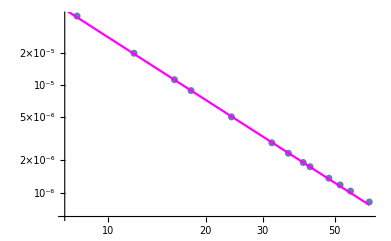

0.00236154/x^1.93103

```mathematica
QuartFit=NonlinearModelFit[CRRMS[[3;;]],a*x^-c,{a, c},x];
f1=ListLogLogPlot[CRRMS];
f2=LogLogPlot[QuartFit[x], {x,0,64}, PlotStyle->Magenta];
Show[f1,f2]
Normal[QuartFit]
```

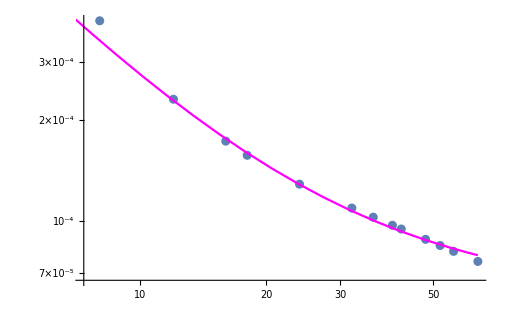

0.000059673+0.00429342/x^1.30041

```mathematica
QuartFit=NonlinearModelFit[du[[2;;]],a*x^-c+b,{a, c, b, d},x];
f1=ListLogLogPlot[du];
f2=LogLogPlot[QuartFit[x], {x,0,64}, PlotStyle->Magenta];
Show[f1,f2]
Normal[QuartFit]
```

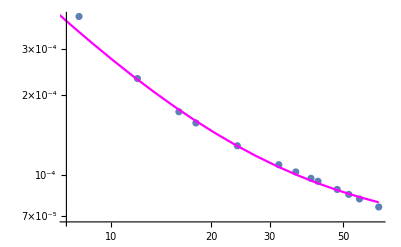

0.00429342/x^1.30041+0.0000604696/x^0.00380671

```mathematica
QuartFit=NonlinearModelFit[du[[2;;]],0.004293417361696581*x^-1.300410378615204+b*x^-a,{a,b, c, d},x];
f1=ListLogLogPlot[du];
f2=LogLogPlot[QuartFit[x], {x,0,64}, PlotStyle->Magenta];
Show[f1,f2]
Normal[QuartFit]
```

```mathematica
data = Import["prerefined.txt", "table"];
```

```mathematica
ARMS=data[[All, {1, 8}]];
PRMS=data[[All, {1, 9}]];
CRRMS=data[[All, {1, 10}]];
du = data[[All, {1, -4}]];
```

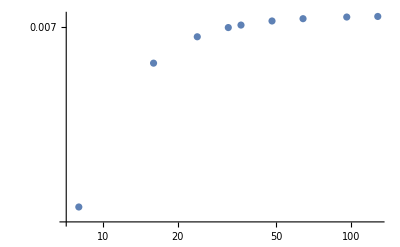

```mathematica
ListLogLogPlot[ARMS]
```

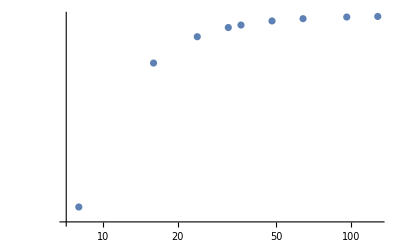

```mathematica
ListLogLogPlot[PRMS]
```

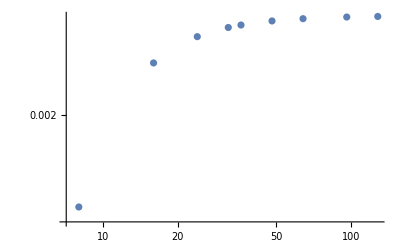

```mathematica
ListLogLogPlot[CRRMS]
```

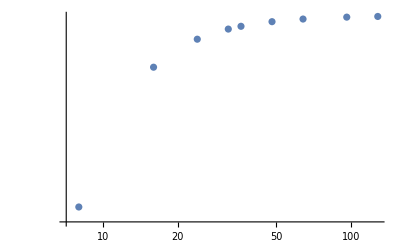

```mathematica
ListLogLogPlot[du]
```